```mathematica
g[y_]:={{1,0},{0,1+(z'[y])^2}}
```

```mathematica
detg[y_]:=Det[g[y]]
```

```mathematica
sqrtdetg[y_]:=Sqrt[detg[y]]
```

```mathematica
H[y_]:=1/2/( detg[y])^(3/2)z''[y]
```

```mathematica
σ[y_]:=σ0
```

```mathematica
(*solve for n^i omega_i == ψTOP at \partial \Omega_TOP*)
```

```mathematica
solTOP=Flatten[Solve[1/sqrtdetg[y] z'[y]==ψTOP,z'[y]]][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→-ψTOP/(√(1-ψTOP^2))

```mathematica
solBOTTOM=Flatten[Solve[-1/sqrtdetg[y] z'[y]==ψBOTTOM,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψBOTTOM/(√(1-ψBOTTOM^2))

```mathematica
L=10;
h=1;
κ=1;
σ0=1;
CC=1/10;
DD=1/2;
ϕTOP=CC;
ϕBOTTOM=0;
ψTOP=DD;
ψBOTTOM=0;
```

```mathematica
eq={κ(-(1/sqrtdetg[y])D[H'[y]/sqrtdetg[y],y]-2( H[y])^3)+ σ [y]H[y]==0}//FullSimplify
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0}

```mathematica
bcs={z[0]==ϕBOTTOM,z[h]==ϕTOP,z'[0]==(z'[y]/.solBOTTOM),z'[h]==(z'[y]/.solTOP)}
```

{z[0]==0,z[1]==1/10,z'[0]==0,z'[1]==-1/(√3)}

```mathematica
sys=Flatten[{eq,bcs}]
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0,z[0]==0,z[1]==1/10,z'[0]==0,z'[1]==-1/(√3)}

```mathematica
sol=NDSolve[sys,z,{y,0,h},WorkingPrecision->10]
```

{{z→InterpolatingFunction[…]}}

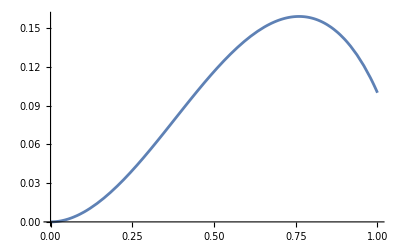

```mathematica
plotzexact=Plot[Evaluate[z[y]/.sol],{y,0,h},PlotRange->All]
```

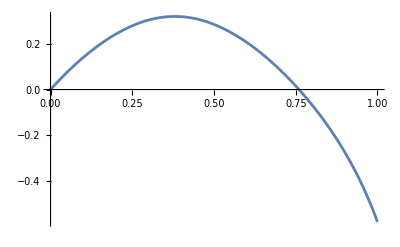

```mathematica
plotωexact=Plot[Evaluate[z'[y]/.sol],{y,0,h},PlotRange->All]
```

```mathematica
tabz=Table[{y,Evaluate[z[y]/.sol][[1]]},{y,0,h,h/10}]
tabω=Table[{y,Evaluate[z'[y]/.sol][[1]]},{y,0,h,h/10}]
```

{{0,0.},{1/10,0.00731337246},{1/5,0.0267435287},{3/10,0.054392179},{2/5,0.0858601227},{1/2,0.116365079},{3/5,0.141231127},{7/10,0.156276672},{4/5,0.157697811},{9/10,0.141238932},{1,0.0999766435}}

{{0,0.},{1/10,0.139934471},{1/5,0.2422526},{3/10,0.303365},{2/5,0.3179302},{1/2,0.2843005},{3/5,0.206069688},{7/10,0.0886313},{4/5,-0.0669971},{9/10,-0.27277},{1,-0.577468984}}

```mathematica
NN=3;
```

```mathematica
fz[y_]:=Sum[c[i]y^i,{i,0,NN}]
fω[y_]:=Sum[d[i]y^i,{i,0,NN}]
```

```mathematica
fitz=FindFit[tabz,fz[y],Table[c[i],{i,0,NN}],y]
fitω=FindFit[tabω,fω[y],Table[d[i],{i,0,NN}],y]
```

{c[0]→0.0000300371897,c[1]→-0.00524403086,c[2]→0.844347452,c[3]→-0.738886103}

{d[0]→0.00259787,d[1]→1.56084,d[2]→-1.82945,d[3]→-0.299034}

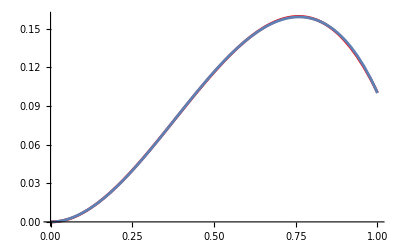

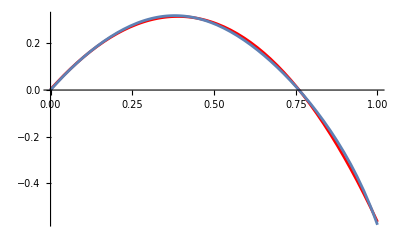

```mathematica
Show[Plot[fz[y]/.fitz,{y, 0,h},PlotStyle->Red],plotzexact]
Show[Plot[fω[y]/.fitω,{y, 0,h},PlotStyle->Red],plotωexact]
```

```mathematica
t=Import["~/Documents/finite_elements/solution/z.csv"];
t=Table[{t[[i,3]],If[Abs[t[[i,2]]-L/2]<0.1,t[[i,1]],0]},{i,2,Length[t]}]
```

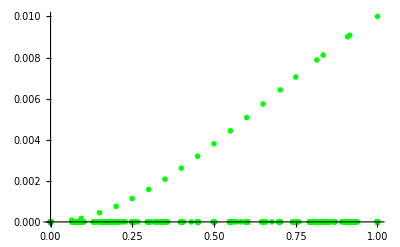

```mathematica
plotnum=ListPlot[t,PlotStyle->{Green,PointSize->0.01}]
```

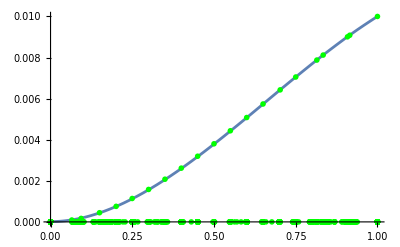

```mathematica
Show[plotexact,plotnum]
```